# Mathematical Statistics

谢泽健

11810105

Chap1

2019.10.4

68.

假设事件A,B,C分别为

A=a>1

B=b>1

C=a<1

容易验证这是一个反例

71.

A∩B 和 C :

A,B,C 相互独立, 则:

P(A∩B∩C)=P(A)P(B)P(C)

于是

P((A∩B)∩C)=P(A)P(B)P(C)

注意到

P((A∩B))≥P(A)P(B)

P((A ∩ B) ∩ C)≥P((A∩B))P(C)

即

P((A ∩ B) ∩ C)≥P(A∩B)P(C)≥P(A)P(B)P(C)

由已知得, 不等号均取等号,于是

P((A ∩ B) ∩ C)=P((A∩B))P(C)

这表明 A∩B 和 C 是独立的.

A∪B 和 C :

要证明

P((A∪B)∩C)=P(A∪B)P(C)

其中

P(A∪B)P(C)=(P(A)+P(B)-P(A∩B))P(C)

由于A∩B 和 C 独立:

P((A ∩ B) ∩ C)=P(A∩B)P(C)=P(A)P(B)P(C)

所以

P(A∩B)=P(A)P(B)⇒A,B独立

同理可得

A,C 相互独立, B,C相互独立

那么

P(A∪B)P(C)=(P(A)+P(B)-P(A∩B))P(C)

=P(A)P(C)+P(B)P(C)-P(A∩B)P(C)=P(A∩C)+P(B∩C)-P(A∩B∩C)

另一方面

P((A∪B)∩C)=P((A∩C)∪(A∩C))

由容斥原理, 展开即证

74.

记五个零件从左到右, 从上到下的顺序损坏的事件为 A_1,A_2,A_3,A_4,A_5:

P((A_1∩A_2)∪(A_3∩A_4)∪A_5)=P(A_5)+P(A_1)·P(A_2)+P(A_3)·P(A_4)-P(A_1)·P(A_2)·P(A_3)·P(A_4)-P(A_1)·P(A_2)·P(A_5)-P(A_3)·P(A_4)·P(A_5)+P(A_1)·P(A_2)·P(A_3)·P(A_4)·P(A_5)=p+2 p^2-2 p^3-p^4+p^5

77.

扔 n 次从未命中靶心的概率为:

P(n)=(1-0.05)^n

求解

1-(1-0.05)^n=0.5

得

n≃13.5134≃14

79.

a.

P(AA)=P(aa)=1/2×1/2=1/4

P(Aa)=1/2×1/2+1/2×1/2=1/2

b.

没有疾病意味着他的基因型为 AA 或 Aa

P(Aa|AA∪Aa)=(P(Aa))/(P(AA∪Aa))=(1/2)/(1/2+1/4)=2/3

c.

定义以下事件

Aa_m={父亲的基因型为Aa}

Aa_f={母亲的基因型为Aa}

Aa={第一代的基因型为Aa}

同理定义 AA_m,AA_f,aa,AA

由b知

P(Aa_m)=2/3,P(AA_m)=1/3

由已知

P(Aa_f)=p,P(AA_f)=1-p

从而

P(aa)=P(Aa_m)×P(Aa_f)×1/4=p/6

P(Aa)=P(Aa_m)P(Aa_f)×1/2+P(AA_m)P(Aa_f)×1/2+P(Aa_m)P(AA_f)×1/2=1/3+p/6

P(AA)=1-P(aa)-P(Aa)=2/3-p/3

d.

P(Aa_m|AA∪Aa)=(P(AA∪Aa|Aa_m)P(Aa_m))/(P(AA∪Aa|Aa_m)P(Aa_m)+P(AA∪Aa|AA_m)P(AA_m))

=((1-p+(3p)/4)×2/3)/((1-p+(3p)/4)×2/3+1×1/3)=2/(p-6)+1=(p-4)/(p-6)

1.

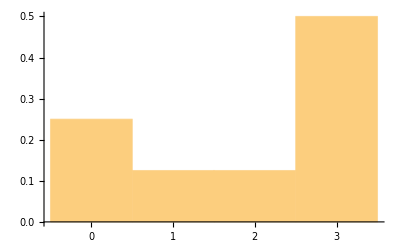

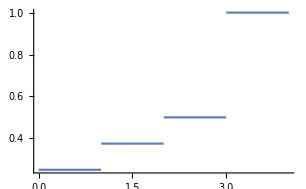

15.

A队在n局中获胜的局数X服从二项分布

X\[Distributed]BinomialDistribution[0.4,n]

在五局三胜制下

P(Win)=P(X≥3)=992/3125≃0.31744

在七局四胜制下

P(Win)=P(X≥4)=4528/15625≃0.289792

故应该选择五局三胜制

31.

a.

在十分钟内, 泊松分布的参数为

λ=2×1/6=1/3

Diane电话响起的次数X服从泊松分布

X\[Distributed]PoissonDistribution[1/3]

故电话响起的概率为

P(X≥1)=1-P(X=0)=1-1/ⅇ^(1/3)=0.283469

b.

在k分钟内,Diane电话响起的次数X服从泊松分布

X\[Distributed]PoissonDistribution[k/30]

要使得电话响起的概率小于0.5, 即

P(X≥1)=1-P(X=0)<0.5

等价于求

P(X=0)=ⅇ^(-k/30)>0.5

所以

k≤30 ln2

补充题

1.

P(X=x)=(2/3)^x